\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## BI-BEZ – Bezpečnost – Lab. cvičení 1 Tomáš Zahradnický, Jiří Buček Katedra počítačových systémů, FIT ČVUT v Praze

Úvod do software Mathematica (opakování)

Substituční šifra

Afinní šifry

Transpoziční šifra

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Velejemny uvod do software Mathematica

Ve cvicenich bude vyuzivano software Mathematica pro demonstraci sifer, jejich kryptoanalyzy, atd., a proto je dulezite se se softwarem Mathematica naucit pracovat alespon na nejake zakladni bazi.

Mathematica je rozdelena na Front End (toto) a Kernel (neni videt). Front End posila prikazy oznacene In[cislo] do kernelu a vystup z kernelu je oznacen Out[cislo]. Prikaz In[cislo] spustite (poslete do kernelu k vyhodnoceni) pomoci klavesove kombinace SHIFT+ENTER, anebo ENTER na numericke klavesnici.

Pred tim, nez zacneme, Mathematica je case sensitive a velmi dba na typ zavorek a proto pozor. Kulate zavorky oznacuji prioritu vyhodnocovani, hranate urcuji argumenty funkce a slozene oznacuji vektory, matice a seznamy. Vice viz dale.

Nyni zkuste vyhodnoti nasledujici vyrazy:

```mathematica
Mod[283,17]
```

```mathematica
Sin[Pi/2]
```

```mathematica
Sum[1/i^2,{i,1,∞}]
```

```mathematica
Mod[102*BEZInverse[102,113],113]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Inicializace worksheetu

Aby bylo mozne pouzit programy v techno slajdech, je nutne provest inicializaci. Klepnete kamkoliv do bloku s programem a nechte ho vyhodnotit.  Block obsahuje definice funkci, ktere budou pouzity pro sifrovani, desifrovani a analyzu. Neni nutne se temitito funkcemi zaobirat.

```mathematica
<<"BarCharts`";
NCharacters=26;
SYMBOLS=Table[FromCharacterCode[65+i],{i,0,57}];
ENGLISH={0.0805726131341181993`1.9999999999999998,0.0125943599170806117`1.9999999999999998,0.0362576759103531896`1.9999999999999976,0.0380959831032189932`1.9999999999999998,0.1146790784996284273`1.9999999999999998,0.0240935581022411703`1.9999999999999998,0.0157233934368521923`1.9999999999999998,0.031212109359721516`1.9999999999999998,0.0741972073375836039`1.9999999999999998,0.001290726326905777`1.9999999999999998,0.0015254038408886455`1.9999999999999998,0.0429459850588649431`1.9999999999999998,0.0222943638283725115`1.9999999999999998,0.0746274494465521962`1.9999999999999998,0.0873782610396213869`1.9999999999999998,0.0389955802401533226`1.9999999999999998,0.0010169358939257637`1.9999999999999976,0.0751750303125122228`1.9999999999999998,0.0571830875738256346`1.9999999999999998,0.0912504400203387179`1.9999999999999998,0.0322290452536472797`1.9999999999999998,0.0081746000704032542`1.9999999999999998,0.0116165369421519928`1.9999999999999976,0.0017991942738686588`1.9999999999999998,0.0243282356162240388`1.9999999999999998,0.0007431454609457504`1.9999999999999998};
VelikostAbecedy[n_Integer]:=Module[{},NCharacters=n;Take[SYMBOLS,n]]
BEZRotChar[x_,amount_]:=FromCharacterCode[Mod[(ToCharacterCode[x]-ToCharacterCode["A"])+amount,NCharacters]+ToCharacterCode["A"]]
AXPBChar[x_,a_,b_]:=FromCharacterCode[Mod[(ToCharacterCode[x]-ToCharacterCode["A"]) a+b,NCharacters]+ToCharacterCode["A"]]
AXPB[x_String,a_,b_]:=StringJoin[(AXPBChar[#1,a,b]&)/@Characters[BEZPrepText[x]]]
AXPBDecrypt[x_String,a_,b_]:=StringJoin[(AXPBCharDecrypt[#1,a,b]&)/@Characters[x]]
BEZZnakPlusB[x_String,b_Integer]:=(BEZRotChar[#1,b]&)/@Characters[x]
AXPBCharDecrypt[x_,a_,b_]:=FromCharacterCode[Mod[((ToCharacterCode[x]-ToCharacterCode["A"])-b) BEZInverse[a,NCharacters],NCharacters]+ToCharacterCode["A"]]
BEZInverse[x_Integer,mod_]:=Inverse[{{x}},Modulus->mod]⟦1⟧⟦1⟧
Caesar[x_String,posun_]:=StringJoin[BEZZnakPlusB[x,posun]]
BEZPrepText[x_String]:=FromCharacterCode[Select[(#1⟦1⟧&)/@ToCharacterCode[Characters[ToUpperCase[x]]],0≤#1-ToCharacterCode["A"]⟦1⟧≤NCharacters&]]
BEZAbsCetnosti[x_String]:=Table[Length[Select[Characters[BEZPrepText[x]],#1===SYMBOLS⟦i⟧&]],{i,1,NCharacters}]
BEZRelCetnosti[x_String]:=N[BEZAbsCetnosti[x]/StringLength[BEZPrepText[x]],2]

RelCetnosti[x_String]:=TableForm[Module[{X},X=BEZRelCetnosti[x];Append[Table[Table[{SYMBOLS⟦7 i+j⟧,X⟦7 i+j⟧},{j,1,7}],{i,0,-1+Floor[NCharacters/7]}],Table[{SYMBOLS⟦7 Floor[NCharacters/7]+i⟧,X⟦7 Floor[NCharacters/7]+i⟧},{i,1,Mod[NCharacters,7]}]]]]
BEZGrafyRelCetnosti[x_String,y_String]:=Module[{RC1,RC2},RC1=BEZRelCetnosti[x];RC2=BEZRelCetnosti[y];BarChart[{RC1,RC2},BarLabels->SYMBOLS,BarEdges->False,BarStyle->{Directive[RGBColor[.1,.2,.7],Opacity[0.7]],Directive[RGBColor[0,.7,0],Opacity[0.7]]},BarSpacing->0.1,Background->GrayLevel[.9]]]
BEZGrafyRelCetnostiSAnglictinou[x_String]:=Module[{RC1,RC2},RC1=BEZRelCetnosti[x];RC2=ENGLISH;BarChart[{RC1,RC2},BarLabels->SYMBOLS,BarEdges->False,BarStyle->{Directive[RGBColor[.1,.2,.7],Opacity[0.7]],Directive[RGBColor[0,.7,0],Opacity[0.7]]},BarSpacing->0.1,Background->GrayLevel[.9]]]
RelCetnostiZBEZRelCetnosti[x_]:=TableForm[{Table[{FromCharacterCode[64+i],x⟦i⟧},{i,7}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,8,14}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,15,21}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,22,26}]}]
Pozice[x_String]:=StringPosition[StringJoin[SYMBOLS],x]⟦1⟧⟦1⟧-1
BEZPadString[x_String,n_Integer]:=If[StringLength[x]<n,BEZPadString[StringJoin[x,"X"],n], If[StringLength[x]==n, x, Abort[]]]
BEZNumToPad[x_String,cols_Integer]:=Floor[(StringLength[x]+cols-1)/cols]*cols
BEZGenerMatrix[x_String,cols_Integer]:=Partition[Characters[BEZPadString[BEZPrepText[x],BEZNumToPad[BEZPrepText[x],cols]]],cols]
Transpozice[x_String,cols_Integer]:=StringJoin[Flatten[Transpose[BEZGenerMatrix[BEZPrepText[x],cols]]]]

Print["Initialization done"]
```

General::obspkg: BarCharts` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Initialization done

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Jednoduche sifry (Caesarova sifra)

Caesarova sifra je znama jako jednoducha substitucni proudova (znakova) sifra, ktera provadi transformaci y = |x+3|_26. Mejme otevreny text (nechte vyhodnotit)

```mathematica
OT:="ANOPENTEXTTHATWILLGETTRANSFORMEDWITHCAESARCIPHER"
```

Zasifrovany text bude:

```mathematica
ST=Caesar[OT,3]
```

DQRSHQWHAWWKDWZLOOJHWWUDQVIRUPHGZLWKFDHVDUFLSKHU

Text lze snadno desifrovat provedenim opacne operace (odectenim) posunu:

```mathematica
Caesar[ST,-3]
```

ANOPENTEXTTHATWILLGETTRANSFORMEDWITHCAESARCIPHER

Kryptoanalyzu teto sifry naleznete na dalsi strance.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalyza Caesarovy sifry

Relativni cetnosti sifroveho textu z minuleho slajdu jsou:

```mathematica
RelCetnosti[ST]
```

A
0.021 | B
0 | C
0 | D
0.1 | E
0 | F
0.042 | G
0.021
H
0.13 | I
0.021 | J
0.021 | K
0.063 | L
0.063 | M
0 | N
0
O
0.042 | P
0.021 | Q
0.063 | R
0.042 | S
0.042 | T
0 | U
0.083
V
0.042 | W
0.15 | X
0 | Y
0 | Z
0.042 |  |

Relativni cetnosti otevreneho textu z minuleho slajdu jsou:

```mathematica
RelCetnosti[OT]
```

A
0.1 | B
0 | C
0.042 | D
0.021 | E
0.13 | F
0.021 | G
0.021
H
0.063 | I
0.063 | J
0 | K
0 | L
0.042 | M
0.021 | N
0.063
O
0.042 | P
0.042 | Q
0 | R
0.083 | S
0.042 | T
0.15 | U
0
V
0 | W
0.042 | X
0.021 | Y
0 | Z
0 |  |

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalyza Caesarovy sifry (2)

Srovnanim relativnich cetnosti (cervena pro sifrovy text, modra pro otevreny text) vidime ze sifra zpusobila posun relativnich cetnosti nasledujicim zpusobem:

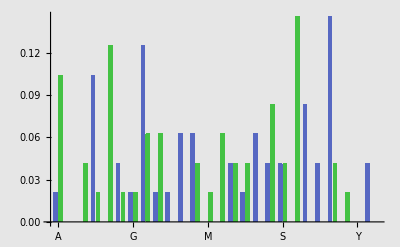

```mathematica
BEZGrafyRelCetnosti[ST,OT]
```

Z grafu vidime, ze pokud zname otevreny text, je velmi snadne uhodnout transformaci, ktera povede k desifrovani textu. Staci jen posunout cetnosti tak, aby grafy splynuly. Pokud otevreny text k dispozici nemame, musime si vystacit napriklad se vzorkem relativnich cetnosti pro jazyk, kterym predpokladame, ze je sifrovy text psan. Predpokladame, ze sifrovy text je psan v anglictive, pro kterou mame relativni cetnosti ulozene v promenne ENGLISH.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalyza Caesarovy sifry (3)

Relativni cetnosti pro anglictinu jsou (ziskano jako relativni cetnosti z cca 20KB souboru):

```mathematica
RelCetnostiZBEZRelCetnosti[ENGLISH]
```

A
0.081 | B
0.013 | C
0.036 | D
0.038 | E
0.11 | F
0.024 | G
0.016
H
0.031 | I
0.074 | J
0.0013 | K
0.0015 | L
0.043 | M
0.022 | N
0.075
O
0.087 | P
0.039 | Q
0.001 | R
0.075 | S
0.057 | T
0.091 | U
0.032
V
0.0082 | W
0.012 | X
0.0018 | Y
0.024 | Z
0.00074 |  |

Nyni muzeme udelat stejny krok, jako v minulem pripade a srovnat relativni cenosti sifroveho textu s relativnimi cetnostmi pro anglictinu:

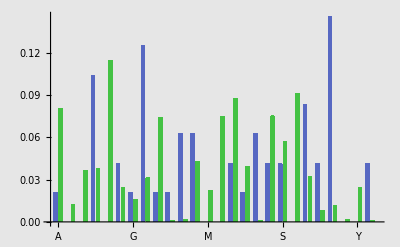

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Ukol 1: Zjistete co se skryva pod nasledujicim sifrovym textem?

Neznamy sifrovy text ST je:

```mathematica
NCharacters=26;
ST="BAGURNGGRZCGAHZOREGUERRABGONQPBATENGHYNGVBAF"
```

BAGURNGGRZCGAHZOREGUERRABGONQPBATENGHYNGVBAF

Provedte analyzu relativnich cetnosti a naleznete k nemu otevreny text. Jde o sifru podobnou Caesarove sifre.

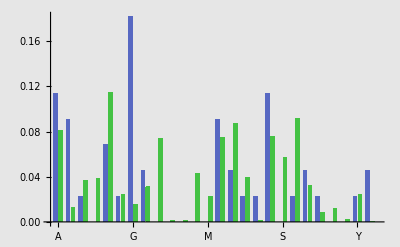

ONTHEATTEMPTNUMBERTHREENOTBADCONGRATULATIONS

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
Caesar[ST,-13]
```

Navod: Srovnejte relativni cetnost. Promenna ST je globalni, takze muzete pouzit pomucky uvedene na predchozich slajdech.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Sifry typu |ap+b|_m

Caesarova sifra je specialnim pripadem afinni sifry |ap+b|_m a je definovana jako |p+b|_m. Sifra tez predstavuje substituci, avsak nyni jiz tato substituce neposunuje graf relativnich cetnosti, ale dochazi k dukladnejsimu "promichani" (viz graf relativnich cetnosti). Celou vec si ukazme na prikladu:

```mathematica
OT="THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER"
```

```mathematica
NCharacters=29
ST=AXPB[OT,6,19]
```

```mathematica
BEZGrafyRelCetnosti[ST,OT]
```

Sifrovy text muzeme desifrovat obracenim sifrovaciho predpisu a to je-li y=|ap+b|_mbude p=|a^-1(y-b)|_m.

```mathematica
AXPB[ST,5,21]
```

Poznamka: Prikazem NCharacters=29 se rozsirila abeceda na 29 symbolu; jejich seznam viz dole.

Vsimnete si, ze jsme pred pouzitim transformace |ap+b|_m rozsirili vstupni abecedu na 29 znaku z 26 pouzitim prirazeni NCharacters=26. Proc byla tato operace nutna a co se stane, kdyz NCharacters zustane 26?
Promenna SYMBOLS obsahuje celou abecedu, ktera muze byt rozsirena az na 58 znaku. Pro vypsani abecedy pouzite pro sifrovani muzeme pouzit funkci softwaru Mathematica Take, ktera vezme prvnich N znaku ze seznamu SYMBOLS, kde N=NCharacters.

```mathematica
Take[SYMBOLS,NCharacters]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Ukol 2: Kryptoanalyza sifry |ap+b|_m

1. Vyberte nahodne konstanty a a b a pro NCharacters=29 s nimi anglicky text alespon o 100 znacich. Takovy text muzete nalezt napriklad v libovolne dokumentaci k software. Az budete mit sifrovy text, poskytnete ho sousedovi (napr. e-mailem) ale nesdelujte mu hodnoty konstant!

```mathematica
NCharacters=29;
OT="NOTICE: This software will not perform or complete any actual financial transactions. You must obtain a separate commercial use license from MindVision to use eSellerate to conduct electronic commerce. Even though it appears to be fully functional, it is not fully functional, IT WILL NOT CONDUCT FINANCIAL TRANSACTIONS, and the software provided under this Agreement is NOT FOR DISTRIBUTION. Under no circumstances shall MindVision be liable for any transactions utilizing the Software under this Evaluation License Agreement.";
a=9;
b=23;
```

```mathematica
ST=AXPB[OT,a,b]
```

YEUIMBU]ILLEKUSXCBSIGGYEUNBCKECPECMEPNGBUBXYHXMUAXGKIYXYMIXGUCXYLXMUIEYLHEAPALUEDUXIYXLBNXCXUBMEPPBCMIXGALBGIMBYLBKCEPPIYVJILIEYUEALBBLBGGBCXUBUEMEYVAMUBGBMUCEYIMMEPPBCMBBJBYU]EAT]IUXNNBXCLUEDBKAGGHKAYMUIEYXGIUILYEUKAGGHKAYMUIEYXGIUSIGGYEUMEYVAMUKIYXYMIXGUCXYLXMUIEYLXYVU]BLEKUSXCBNCEJIVBVAYVBCU]ILXTCBBPBYUILYEUKECVILUCIDAUIEYAYVBCYEMICMAPLUXYMBLL]XGGPIYVJILIEYDBGIXDGBKECXYHUCXYLXMUIEYLAUIGIQIYTU]BLEKUSXCBAYVBCU]ILBJXGAXUIEYGIMBYLBXTCBBPBYU

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Ukol 2: Kryptoanalyza sifry |ap+b|_m (2)

2. Az obdrzite sifrovy text od souseda, priradte jeho hodnotu do promenne ST:

```mathematica
NCharacters=29;
ST="RCBB\\ZFTQICFTWFLF]FBHQFTGQBBFV\\ZVBAK\\ZF]ZNZ]ATQVRFV]AAKQGVW\\ZQTQFBVRQ]AC\\L\\FTFZAFLVZFCL\\THW\\GQLKBQFG[]AAG\\TH\\VWFLVRQVQTVRTFJQGLVABJA[VRQFV]FTV\\ZRCBB\\ZFTQLQFLAT[ABJ\\TH\\TVRQZQTVBF]HC][A[JQD\\ZA\\T]FVQAZVAPQBICFTJAMQGTABVRWFBGF[VQB\\VL[ABJFV\\ATFTGWFLLCPVBAK\\ZF]\\TTFVCBQW\\VR\\VL]FBHQL\\XQATAZVAPQBVRQLVABJPQZFJQFRCBB\\ZFTQBQFZR\\THJFD\\JCJLCLVF\\TQGW\\TGLA[JKRSJRGCQVAVRQ\\T[]CQTZQA[FTCKKQB]QMQ]]AWICFT]AAKQGICLVA[[LACVRQBT]AC\\L\\FTFPQ[ABQJFS\\TH]FTG[F]]TQFBJABHFTZ\\VNATAZVAPQBWQFSQT\\THVAVBAK\\ZF]LVABJLVFVCLAMQB]FTGICFTVCBTQGPFZSVAVRQLACVRQFLVAMQBAKQTWFVQBLZBALL\\THVRQJ\\LL\\LL\\KK\\B\\MQBGQ]VFF[VQBVCBT\\THVAVRQTABVRQFLVVRQLVABJJFGQ\\VL[\\TF]]FTG[F]]ICLVWQLVA[KQTLFZA]F[]AB\\GF]FVQATAZVAPQBICFTZATV\\TCQGUC\\ZS]NVAVRQTABVRFTGWFLFPLABPQGPNFTFKKBAFZR\\THZA]G[BATVF]VRACHR\\VLJA\\LVCBQZATVB\\PCVQGVAFGQFG]N[]AAGQMQTV\\TVRQJ\\GFV]FTV\\ZLVFVQL";
```

Nyni provedte analyzu cetnosti:

```mathematica
RelCetnosti[ST]
```

A
0.087 | B
0.066 | C
0.039 | D
0.0025 | E
0 | F
0.098 | G
0.036
H
0.017 | I
0.0087 | J
0.026 | K
0.019 | L
0.056 | M
0.0075 | N
0.0062
O
0 | P
0.015 | Q
0.096 | R
0.036 | S
0.0062 | T
0.081 | U
0.0012
V
0.1 | W
0.016 | X
0.0012 | Y
0 | Z
0.04 | [
0.026 | \
0.067
]
0.046 |  |  |  |  |  |

A srovnejte ji s cetnostmi pro anglictinu:

```mathematica
RelCetnostiZBEZRelCetnosti[ENGLISH]
```

A
0.081 | B
0.013 | C
0.036 | D
0.038 | E
0.11 | F
0.024 | G
0.016
H
0.031 | I
0.074 | J
0.0013 | K
0.0015 | L
0.043 | M
0.022 | N
0.075
O
0.087 | P
0.039 | Q
0.001 | R
0.075 | S
0.057 | T
0.091 | U
0.032
V
0.0082 | W
0.012 | X
0.0018 | Y
0.024 | Z
0.00074 |  |

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Ukol 2: Kryptoanalyza sifry |ap+b|_m (3)

Z analyzy relativnich cetnosti muzeme zjistit, ze nejcetni pismena pro anglictinu jsou T a E. Toho muzeme pouzit pro zjisteni desifrovaciho klice. Vybereme tedy 2 nejcetnejsi pismena z analyzy sifroveho textu a zkusime je namapovat na T a E. Resenim soustavy 2 rovnic o 2 neznamych vypocteme nezname koeficienty a a b.

Rekneme ze pro nas priklad vidime, ze nejcetnejsi jsou  pismena U a B. Zkusme tedy predpokladat, ze:
	U=|a T+b|_29
	B=|a E+b|_29
Tedy, z T neznamou transformaci vznikne U a z E touz transformaci vznikne B. Abychom urcili a a b, musime uz jen vyresit tyto dve rovnice napriklad dosazovaci metodou:

b=|U-a T|_29
	B = |a E+|U-a T|_29|_29

Protoze nezalezi, kdy redukci mod 29 provedeme, muzeme vztah prepsat jako:
	B = |a ( E - T )+U|_29
	a =|(B-U)*(E-T)^-1|_29
	b = |U-(B-U)*(E-T)^-1 T|_29

Nyni muzeme predpis zkusit (pozn. pokud budete pocitat na papire, nezapomente ze A odpovida 0, B 1, atd.):

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Ukol 2: Kryptoanalyza sifry |ap+b|_m (4)

Pro jednoduchost jsou zde rovnice implementovany do systemu Mathematica a vypoctene konstanty se ulozi do promennych c a d.

```mathematica
c=Mod[(Pozice["B"]-Pozice["U"])*BEZInverse[Pozice["E"]-Pozice["T"],NCharacters],NCharacters]
d=Mod[Pozice["U"]-c*Pozice["T"],NCharacters]
```

9

23

Nyni se muzeme pokusit text desifrovat:

```mathematica
AXPBDecrypt[ST,10,5]
```

HURRICANEJUANWASALARGEANDERRATICTROPICALCYCLONETHATLOOPEDTWICENEARTHELOUISIANACOASTCAUSINGWIDESPREADFLOODINGITWASTHETENTHNAMEDSTORMOFTHEATLANTICHURRICANESEASONFORMINGINTHECENTRALGULFOFMEXICOINLATEOCTOBERJUANMOVEDNORTHWARDAFTERITSFORMATIONANDWASSUBTROPICALINNATUREWITHITSLARGESIZEONOCTOBERTHESTORMBECAMEAHURRICANEREACHINGMAXIMUMSUSTAINEDWINDSOFMPHKMHDUETOTHEINFLUENCEOFANUPPERLEVELLOWJUANLOOPEDJUSTOFFSOUTHERNLOUISIANABEFOREMAKINGLANDFALLNEARMORGANCITYONOCTOBERWEAKENINGTOTROPICALSTORMSTATUSOVERLANDJUANTURNEDBACKTOTHESOUTHEASTOVEROPENWATERSCROSSINGTHEMISSISSIPPIRIVERDELTAAFTERTURNINGTOTHENORTHEASTTHESTORMMADEITSFINALLANDFALLJUSTWESTOFPENSACOLAFLORIDALATEONOCTOBERJUANCONTINUEDQUICKLYTOTHENORTHANDWASABSORBEDBYANAPPROACHINGCOLDFRONTALTHOUGHITSMOISTURECONTRIBUTEDTOADEADLYFLOODEVENTINTHEMIDATLANTICSTATES

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Transpozice

Substituce zpusobuje konfuzi nahradou jednoho znaku znakem jinym a sifry zalozene na ni jsou zranitelne frekvencni analyzou. Proto obvykle substituci kombinujeme s transpozici, ktera preskupuje poradi pismen v textu (difuze). To se v praxi provadi zapsanim otevreho textu do matice po radcich a precteni po sloupcich. Ukazme si to na priklade textu "PLEASE SEND MONEY", ktery nejdrive doplnime vyplni (X) na delku, ktera obsadi celou matici. Tak ziskame matici:
("P" | "L" | "E" | "A" | "S" | "E"
"S" | "E" | "N" | "D" | "M" | "O"
"N" | "E" | "Y" | "X" | "X" | "X"), kterou transponujeme ("P" | "S" | "N"
"L" | "E" | "E"
"E" | "N" | "Y"
"A" | "D" | "X"
"S" | "M" | "X"
"E" | "O" | "X") a precteme text po radcich, cimz dostavame:
PSNLEEENYADXSMXEOX. V kombinaci se substituci napriklad pomoci afinni sifry je vysledna sifra posilena. Transpozici si muzete vyzkouset volanim funkce Transpozice[retezec, pocet sloupcu]:

```mathematica
NCharacters=26;
ST=Transpozice["THE GOLD IS BURIED IN ORONO",6]
```

TDIRHIEOESDNGBIOOUNXLROX

Pokud bychom chteli videt matici, muzete pouzit funkci BEZGenerMatrix[retez, pocet sloupcu]. Tim zaroven uvidime mnozstvi vyplne, ktere se pridalo na zarovnani na potrebnou delku.

```mathematica
BEZGenerMatrix["THE GOLD IS BURIED IN ORONO",6]//MatrixForm
```

(T | H | E | G | O | L
D | I | S | B | U | R
I | E | D | I | N | O
R | O | N | O | X | X)

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Transpozice (2)

Detranspozice se provadi obracenim predpisu, tedy zadanim poctu radku vysledne matice:

```mathematica
OT=Transpozice[ST,4]
```

THEGOLDISBURIEDINORONOXX

Je zrejme, ze transpozice NEMA vliv na frekvencni usporadani a graf otevreneho i sifroveho textu bude pro analyzu relativni cetnosti naprosto identiticky. To si muzeme ukazat v nasledujicim prikladu:

```mathematica
OT
ST
```

THEGOLDISBURIEDINORONOXX

TDIRHIEOESDNGBIOOUNXLROX

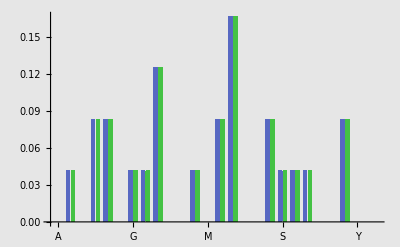

```mathematica
BEZGrafyRelCetnosti[OT,ST]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalyza transpozice

Kryptoanalyzu transpozicni sifry provadime na zaklade bigramove analyzy. V sifrovem textu hledame bigramy avsak mezi jednotlivymi znaky bigramu byva zpravidla nekolik (nekdy mnoho) dalsich znaku. Pro anglictinu je typicke hledat bigramy s nejvetsi cetnosti, coz jsou: TH, HE, AN, RE, ER, IN, ON, AT, ND, ST, ES, EN, OF, TE a ze vzdalenosti znaku bigramu se snazime stanovit parametry transpozice, ktere byly pouzity. Pro sifrovy text TDIRHIEOESDNGBIOOUNXLROX vidime ihned bigramy TH a HE z cehoz usoudime, ze mela matice 4 radky:

```mathematica
Transpozice["TDIRHIEOESDNGBIOOUNXLROX",4]
```

THEGOLDISBURIEDINORONOXX

Dalsi moznosti je faktorizovat delku textu a tim zjistit vsechny delitele delky textu a postupne je zkusit.

```mathematica
FactorInteger[StringLength["TDIRHIEOESDNGBIOOUNXLROX"]]/.{x_Integer,y_Integer}->HoldForm[x^y]
```

{2^3,3^1}

Zde tento pripad vidime, ze delka textu je 24 znaku. Z toho muzeme usoudit, ze pro transpozice mohla byt: 2*12, 3*8, 4*6, 6*4, 8*3, 12*2. Jine kombinace neexistuji. Pro nas pripad byla pouzita transpozice 6*4.

Pokud text nebyl tak dlouhy, jak byl zadan predpis, musel byt doplnen vyplni (padding). Ze znalosti funkce, ktera transpozici provadi vime, ze tato funkce doplnuje na konec textu pismena X, dokud nezarovna text na potrebnou delku a to je skutecnost, kterou muzeme vyuzit k prolomeni transpozice, protoze vzdalenost teto vyplne (zvlaste v pripade, ze bylo doplneno vice znaku X) udava transpozicni konstantu, ktera byla pouzita pri sifrovani. Delka textu/tato konstanta udava detranspozicni konstantu.

Pro nas text vidime, ze vzdalenost paddingu X je 4 znaky, z cehoz rovnou plyne konstanta pro detranspozici.

Upozorneni: Pokud byla transpozice pouzita vicenosobne, je jeji kryptoanalyza znacne obtiznejsi!!

```mathematica
Transpozice[Transpozice["THEGOLDISBURIEDINORONO",4],3]
```

TIHEEDGIONLODRIOSNBOUXRX

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Ukol 3: Kryptoanalyza transpozice

Napiste kus anglickeho textu o delce 30-50 znaku a nahodne zvolte transpozicni konstantu. Provedte nad timto textem transpozici s vami zvolenou konstantou a vysledny sifrovy text poslete sousedovi.

```mathematica
OT="DEFEATTHETRANSPOSITIONCHALLENGE"
```

DEFEATTHETRANSPOSITIONCHALLENGE

```mathematica
Transpozice[OT,9]
```

DTTEERINFAOGENNEASCXTPHXTOAXHSLXEILX

Az obdrzite text od souseda, priradte ho to teto promenne:

```mathematica
ST="DTTEERINFAOGENNEASCXTPHXTOAXHSLXEILX"
```

DTTEERINFAOGENNEASCXTPHXTOAXHSLXEILX

Nyni se snazte zjistit, jakou transpozici vas soused pouzil. Vyuzijte metod popsanych na minulem slajdu. Pro jednoduchost faktorizaci opakujeme nyni pro promennou sifroveho textu:

```mathematica
FactorInteger[StringLength[ST]]/.{x_Integer,y_Integer}->HoldForm[x^y]
```

{2^2,3^2}

```mathematica
Transpozice[ST,4]
```

DEFEATTHETRANSPOSITIONCHALLENGEXXXXX